```mathematica
(*
ст.гр.221703
Воложинец Архип
Вариант 3
*)
```

```mathematica
(*Задание 1*)
```

```mathematica
f[x_]:= (Log[Cos[x+4]]^2)^(1/3);
Subscript[x, 0]=1.82;
graph=Plot[f[x],{x,-6,5},PlotStyle->Magenta];
```

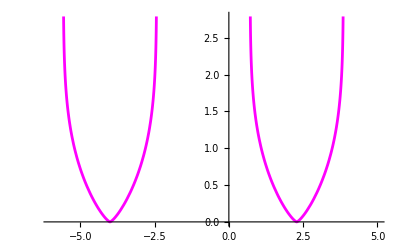

```mathematica
Show[graph]
```

```mathematica
(*1.a*)
```

```mathematica
d11=D[f[x],x]/.x->Subscript[x, 0]
d21=D[f[x],{x,2}]/.x->Subscript[x, 0]
```

-0.692084

0.696623

```mathematica
(*1.б*)
FiniteDiff1[y_,y1_]:=y1-y;
FiniteDiff2[y_,y1_,y2_]:=y2-2y1+y;
FiniteDiff3[y_,y1_,y2_,y3_]:=y3-3y2+3y1-y;
```

```mathematica
(*Шаг h = 0.1*)
h=0.1
```

0.1

```mathematica
y1=1/h(FiniteDiff1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FiniteDiff2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FiniteDiff3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]])
```

-0.690232

```mathematica
y2=1/h^2(FiniteDiff2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FiniteDiff3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]])
```

0.632285

```mathematica
{Abs[d11-y1],Abs[d21-y2]}
```

{0.00185118,0.0643387}

```mathematica
(*Шаг h = 0.01*)
```

```mathematica
h=0.01
```

0.01

```mathematica
y1=1/h(FiniteDiff1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FiniteDiff2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FiniteDiff3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]])
y2=1/h^2(FiniteDiff2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FiniteDiff3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]])
```

-0.692083

0.696211

```mathematica
{Abs[d11-y1],Abs[d21-y2]}
```

{1.126×10^-6,0.000411991}

```mathematica
(*При уменьшении шага результат получается более точным*)
```

```mathematica
(*Задание 2*)
```

```mathematica
(*2.a*)
f[x_]:=Tan[1+Cosh[1/(x+2)]]^2
```

```mathematica
h=0.2;
a=-1;
b=3;
data=Table[{x,(f[x+h]-f[x-h])/(2h)},{x,a,b,h}];
TableForm[data,TableHeadings->{Table[i,{i,(b-a)/h+1}],{"x_i","y'_i"}}]
```

| x_i | y'_i
1 | -1. | 2.21937
2 | -0.8 | 2.42858
3 | -0.6 | 2.29713
4 | -0.4 | 2.04518
5 | -0.2 | 1.7668
6 | 0. | 1.50402
7 | 0.2 | 1.27258
8 | 0.4 | 1.07562
9 | 0.6 | 0.910864
10 | 0.8 | 0.774099
11 | 1. | 0.660835
12 | 1.2 | 0.566951
13 | 1.4 | 0.488915
14 | 1.6 | 0.423798
15 | 1.8 | 0.369213
16 | 2. | 0.323234
17 | 2.2 | 0.28431
18 | 2.4 | 0.251195
19 | 2.6 | 0.222881
20 | 2.8 | 0.198558
21 | 3. | 0.177566

```mathematica
(*2.б*)
```

```mathematica
derivateOfFunc=D[f[x],x]
```

-(2 Sec[1+Cosh[1/(2+x)]]^2 Sinh[1/(2+x)] Tan[1+Cosh[1/(2+x)]])/(2+x)^2

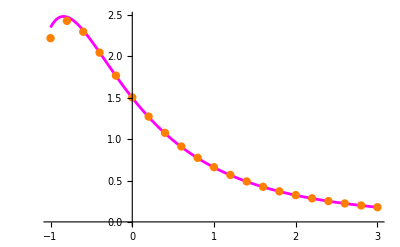

```mathematica
graph=Plot[derivateOfFunc,{x,-1,3},PlotStyle->Magenta];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Orange}];
Show[graph,dots]
```

```mathematica
(*Задание 3*)
(*3.а*)
```

```mathematica
f[x_]:=(2+(3x+1,7)^(1/4))/(x+√(1.5 x^2+1));
```

```mathematica
a=0.3;
b=0.9;
n1=8;
Subscript[x, 0]=a;
step=(b-a)/n1;
```

```mathematica
For[i=1,i<=n1,i++,Subscript[x, i]=step+Subscript[x, i-1];]
```

```mathematica
averageRectangle1=(b-a)/n1*∑_(i=1)^n1 f[Subscript[x, i-1]+(b-a)/(2*n1)]
```

1.96522

```mathematica
n2=10;
step=(b-a)/n2;
For[i=1,i<=n2,i++,Subscript[x, i]=step+Subscript[x, i-1];]
```

```mathematica
averageRectangle2=(b-a)/n2*∑_(i=1)^n2 f[Subscript[x, i-1]+(b-a)/(2*n2)]
```

1.96518

```mathematica
(*по Ричардсону*)
```

```mathematica
k=2;
Richardson=averageRectangle2+n1^k/(n2^k-n1^k)(averageRectangle2-averageRectangle1)
```

1.96511

```mathematica
(*3.б*)
```

```mathematica
n1=8;
Subscript[x, 0]=a;
step=(b-a)/n1;
For[i=1,i<=n1,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
trapezoid1=(b-a)/n1*(∑_(i=1)^(n1-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n1]]/2)
```

1.9649

```mathematica
n2=10;
Subscript[x, 0]=a;
step=(b-a)/n2;
For[i=1,i<=n2,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
trapezoid2=(b-a)/n2*(∑_(i=1)^(n2-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n2]]/2)
```

1.96498

```mathematica
(*По Ричардсону*)
```

```mathematica
Richardson=trapezoid2+n1^k/(n2^k-n1^k)(trapezoid2-trapezoid1)
```

1.96511

```mathematica
(*Задание 4*)
```

```mathematica
(*8 частей*)
```

```mathematica
data=({{-1, 0.3499}, {-0.9, 0.3886}, {-0.8, 0.4317}, {-0.7, 0.4795}, {-0.6, 0.5325}, {-0.5, 0.5915}, {-0.4, 0.6570}, {-0.3, 0.7297}, {-0.2, 0.8105}});
```

```mathematica
a=-1;
b=-0.2;
n=4;
h=(b-a)/(2n)
```

0.1

```mathematica
For[i=0,i<=2*n,i++,Subscript[y, i]=data[[i+1,2]];]
```

```mathematica
SimpsonFormula=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.438667

```mathematica
(*16 частей*)
```

```mathematica
data=({{-1, 0.3499}, {-0.95, 0.4055}, {-0.9, 0.3886}, {-0.85, 0.4459}, {-0.8, 0.4317}, {-0.75, 0.4904}, {-0.7, 0.4795}, {-0.65, 0.5392}, {-0.6, 0.5325}, {-0.55, 0.5930}, {-0.5, 0.5915}, {-0.45, 0.6521}, {-0.4, 0.6570}, {-0.35, 0.7171}, {-0.3, 0.7297}, {-0.25, 0.7885}, {-0.2, 0.8105}});
```

```mathematica
n=8;
h=(b-a)/(2n)
For[i=0,i<=2*n,i++,Subscript[y, i]=data[[i+1,2]];]
```

0.05

```mathematica
SimpsonFormula=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.455137

```mathematica
(*Задание 5*)
```

```mathematica
f[x_]= Cos[5x+2]/x
```

Cos[2+5 x]/x

```mathematica
a=0.8;
b=2.1;
n=7;
LegendreP[n,t]
```

1/16 (-35 t+315 t^3-693 t^5+429 t^7)

```mathematica
sl=NSolve[LegendreP[n,t]==0,t]
```

{{t→-0.949108},{t→-0.741531},{t→-0.405845},{t→0.},{t→0.405845},{t→0.741531},{t→0.949108}}

```mathematica
tt=t/.sl
```

{-0.949108,-0.741531,-0.405845,0.,0.405845,0.741531,0.949108}

```mathematica
T=Table[If[i==1,1,(tt[[j]])^(i-1)],{i,n},{j,n}];MatrixForm[T]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
-0.949108 | -0.741531 | -0.405845 | 0. | 0.405845 | 0.741531 | 0.949108
0.900806 | 0.549868 | 0.16471 | 0. | 0.16471 | 0.549868 | 0.900806
-0.854962 | -0.407745 | -0.0668469 | 0. | 0.0668469 | 0.407745 | 0.854962
0.811451 | 0.302355 | 0.0271295 | 0. | 0.0271295 | 0.302355 | 0.811451
-0.770155 | -0.224206 | -0.0110104 | 0. | 0.0110104 | 0.224206 | 0.770155
0.73096 | 0.166256 | 0.0044685 | 0. | 0.0044685 | 0.166256 | 0.73096)

```mathematica
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N
```

{2.,0.,0.666667,0.,0.4,0.,0.285714}

```mathematica
A=LinearSolve[T,B]
```

{0.129485,0.279705,0.38183,0.417959,0.38183,0.279705,0.129485}

```mathematica
int=(b-a)/2*∑_(i=1)^n A[[i]]*f[(b+a)/2+(b-a)/2*tt[[i]]]
```

0.0969024

```mathematica
PaddedForm[int, {19,18}]
```

0.096902358500152500